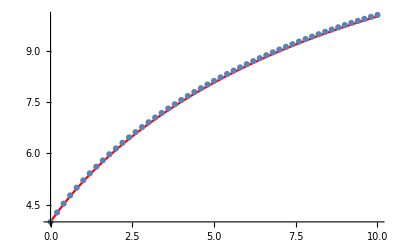

```mathematica
ClearAll["Global`*"]

j=1;a={1,2,3};
Do[ 
n0=4;ro=1.225;ts=0;tf=10;A=.33;p=400;c=1;m=70;

tl=Range[ts,tf,dt];
ll=Length[tl];
nl=0tl;
nl[[1]]=n0;
Do[nl[[j]]=nl[[j-1]]+p dt/(m *nl[[j-1]])-c ro A dt nl[[j-1]]^2/(2 m), {j,2,ll}];mtable=Table[{tl[[i+1]],nl[[i+1]]},{i,0,ll-1}];a[[j]]=ListPlot[mtable,PlotStyle->Thin,PlotStyle->PointSize[.01]];
j=j+1
,{dt,{.5,.2,.05}}]
s=NDSolve[{y'[x]== p/(y[x] m)-c ro A y[x]^2/(2 m),y[0]==4},y,{x,ts,tf}];
Show[Plot[Evaluate[y[x]/.s],{x,ts,tf},PlotStyle->Red],a[[2]]]
```

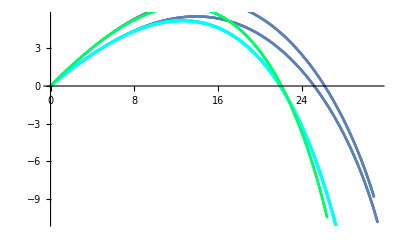

```mathematica
(*problem 2.9*)

prob2[θ_]:=(
y0=1.0 10^4;pos={};ve={};j=1;y0=1.0 10^4;
g=9.8;tm=100;v0=700.; b=4*10^-5;ts=0;tf=100;dt=.1;

tl=Range[ts,tf,dt];
ll=Length[tl];
xl=0tl;
xl[[1]]=0;
yl=0 tl;
yl[[1]]=0;
vx=0 tl;vy=0 tl;
vx[[1]]=v0 Cos[θ Pi/180];vy[[1]]=v0 Sin[θ Pi/180];
α=2.5;β=6.5*10^-3/288;

Do[v=Norm[{vx[[j-1]],vy[[j-1]]}]; ρ=  E^((- 1*yl[[j-1]])/y0) ;
vx[[j]]=vx[[j-1]]-b  v vx[[j-1]] ρ dt;
xl[[j]]=xl[[j-1]]+vx[[j-1]] dt;
vy[[j]]=vy[[j-1]]-g dt - b v vy[[j-1]] dt ρ ;
yl[[j]]=yl[[j-1]] +vy[[j-1]] dt; , {j,2,ll}];
(*Know we find the range*) FindRange[yl_]:=(Do[If[yl[[i]]<=0,m=xl[[i]]; End],{i,1,Length[xl]}];m);
Rang=FindRange[yl]/1000
ListPlot[Table[{xl[[j]],yl[[j]]}/1000,{j,1,ll}]]);
prob22[θ_,co_]:=((*without atmosphere efefcts*)
y0=1.0 10^4;pos={};ve={};j=1;y0=1.0 10^4;
g=9.8;tm=100;v0=700.; b=4*10^-5;ts=0;tf=100;dt=.1;

tl=Range[ts,tf,dt];
ll=Length[tl];
xl=0tl;
xl[[1]]=0;
yl=0 tl;
yl[[1]]=0;
vx=0 tl;vy=0 tl;
vx[[1]]=v0 Cos[θ Pi/180];vy[[1]]=v0 Sin[θ Pi/180];


Do[v=Norm[{vx[[j-1]],vy[[j-1]]}]; 
vx[[j]]=vx[[j-1]]-b  v vx[[j-1]]  dt;
xl[[j]]=xl[[j-1]]+vx[[j-1]] dt;
vy[[j]]=vy[[j-1]]-g dt - b v vy[[j-1]] dt  ;
yl[[j]]=yl[[j-1]] +vy[[j-1]] dt; , {j,2,ll}];
(*Know we find the range*) FindRange[yl_]:=(Do[If[yl[[i]]<=0,m=xl[[i]]; End],{i,1,Length[xl]}];m);
Rang=FindRange[yl]/1000
ListPlot[Table[{xl[[j]],yl[[j]]}/1000,{j,1,ll}],PlotStyle->Hue[co/10]]);

Show[{prob2[35][[2]], prob2[40][[2]], prob22[35,5][[2]], prob22[40,4][[2]]}] (*without green , with blue*)
```

```mathematica
ranges=Table[prob2[th][[1]],{th,30,50}];p=Position[ranges,Max[ranges]]; maxangel=30+p
```

{{35}}

```mathematica
3
```

3

```mathematica
ClearAll["Global`*"]
trajc[θ_,vwind_,c_]:=(pos={};ve={};j=1;
g=9.8;tm=100;v0=110 0.447;ts=0;tf=40;dt=.1;

tl=Range[ts,tf,dt];
ll=Length[tl];
xl=0tl;
xl[[1]]=0;
yl=0 tl;
yl[[1]]=0;
vx=0 tl;vy=0 tl;
vx[[1]]=v0 Cos[θ Pi/180];vy[[1]]=v0 Sin[θ Pi/180];Δ =5; vd=35;
A[vx_,vy_]:=0.0039 + 0.0058/(1+ E^((((vx)^2+vy^2)^0.5-vd)/Δ));


Do[ax=Norm[{vx[[j-1]]-vwind,vy[[j-1]]}] (vx[[j-1]] -vwind);
ay=Norm[{vx[[j-1]]-vwind,vy[[j-1]]}] vy[[j-1]];
 
vx[[j]]=vx[[j-1]]-A[vx[[j-1]],vy[[j-1]]]  ax dt;
xl[[j]]=xl[[j-1]]+vx[[j-1]] dt;
vy[[j]]=vy[[j-1]]-g dt - A[vx[[j-1]],vy[[j-1]]] ay dt ;
yl[[j]]=yl[[j-1]] +vy[[j-1]] dt; If[yl[[j]]<=0,Break[]];, {j,2,ll}];

{ListPlot[Table[{xl[[j]],yl[[j]]},{j,1,ll/2}],PlotStyle->Hue[c/10],PlotStyle->PointSize[.0001]]
,Max@xl});
```

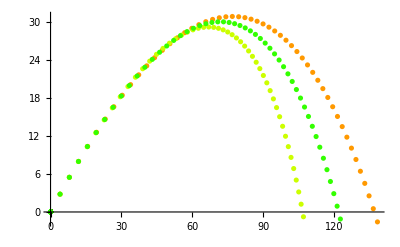

```mathematica
Show[trajc[35,10  0.447,1][[1]],trajc[35,-10 0.447 ,2][[1]],trajc[35,0,3][[1]]]
(*PlotLegends->{"Tail","head","no wind"}*)
```

a for different angeles:

```mathematica
ranges=Table[trajc[th,10  0.447,1][[2]],{th,30,50}];
Position[ranges,Max[ranges]]+30
```

{{39}}

b for different wind

```mathematica
ranges=Table[trajc[th,25,1][[2]],{th,20,50}];
Position[ranges,Max[ranges]]+20
```

{{46}}

```mathematica
c range v vs
```

c range v vs

```mathematica
trajc1[v0_,vwind_,c_]:=(pos={};ve={};j=1; θ=35;
g=9.8;tm=100;ts=0;tf=40;dt=.1;

tl=Range[ts,tf,dt];
ll=Length[tl];
xl=0tl;
xl[[1]]=0;
yl=0 tl;
yl[[1]]=0;
vx=0 tl;vy=0 tl;
vx[[1]]=v0 Cos[θ Pi/180];vy[[1]]=v0 Sin[θ Pi/180];Δ =5; vd=35;
A[vx_,vy_]:=0.0039 + 0.0058/(1+ E^((((vx)^2+vy^2)^0.5-vd)/Δ));


Do[ax=Norm[{vx[[j-1]]-vwind,vy[[j-1]]}] (vx[[j-1]] -vwind);
ay=Norm[{vx[[j-1]]-vwind,vy[[j-1]]}] vy[[j-1]];
 
vx[[j]]=vx[[j-1]]-A[vx[[j-1]],vy[[j-1]]]  ax dt;
xl[[j]]=xl[[j-1]]+vx[[j-1]] dt;
vy[[j]]=vy[[j-1]]-g dt - A[vx[[j-1]],vy[[j-1]]] ay dt ;
yl[[j]]=yl[[j-1]] +vy[[j-1]] dt; If[yl[[j]]<=0,Break[]];, {j,2,ll}];

{ListPlot[Table[{xl[[j]],yl[[j]]},{j,1,ll/2}],PlotStyle->Hue[c/10],PlotStyle->PointSize[.0001]]
,Max@xl})
```

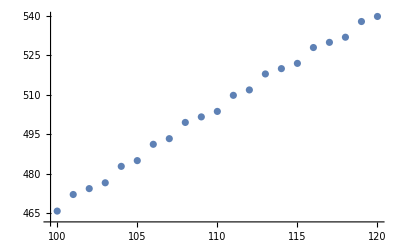

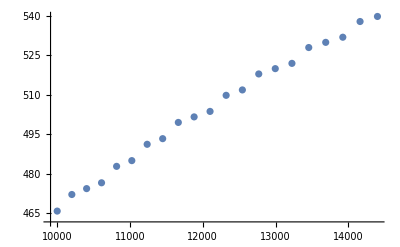

```mathematica
ranges0=Table[{th,trajc1[th,25,1][[2]]},{th,100,120}];ranges1=Table[{th^2,trajc1[th,25,1][[2]]},{th,100,120}];
ListPlot[{ranges0}]
ListPlot[ranges1]
```

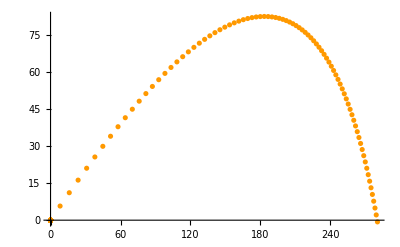
{-Graphics-,280.309}

```mathematica
(*D*)
trajc1[100,0,1]
```

```mathematica
ind=Do[If[xl[[i]]>60.5* 0.305,y=i;Break[]],{i,1,Length[xl]}]

Norm[{vx[[y]],vy[[y]]}]
```

87.6249